```mathematica
(* CORRELATION ENERGY FITTING TO LOGISTIC FUNCTION *)
```

```mathematica
(* Generating log omegas *)
omega=N[Table[10^i,{i,-4,4}]];
logo=N[Log[Table[10^i,{i,-4,4}]]];
massP={1,1.5,2,3,10,50,207,400,900,1836};
(* correlation energies for m=1 using variation method*)
(*{-0.141337,-0.140006,-0.128294,-0.086137,-0.059918,-0.052581,-0.050455,-0.049803,-0.049605}*)
set[1]= {-0.141337,-0.140006,-0.128294,-0.086160,-0.060066,-0.052768,-0.050650,-0.049998,-0.049804};

(* correlation energies for m=1.5 using variation method*)
(*{-0.168189,-0.166854,-0.154850,-0.105994,-0.071490,-0.061655,-0.058820,-0.057948,-0.057773}*)
set[2]={-0.168189,-0.166854,-0.154850,-0.106014,-0.071659,-0.061878,-0.059054,-0.058182,-0.058010} ;

(* correlation energies for m=2 using variation method*)
(*{-0.183855,-0.182519,-0.170363,-0.117354,-0.076839,-0.065106,-0.061727,-0.060689,-0.060368}*)
set[3]={-0.183855,-0.182519,-0.170363,-0.117372,-0.077021,-0.065352,-0.061987,-0.060948,-0.060632} ;

(* correlation energies for m=3 using variation method*)
(*{-0.199277,-0.197939,-0.185627,-0.127779,-0.079392,-0.065147,-0.061064,-0.059814,-0.059435}*)
set[4]= {-0.199277,-0.197939,-0.185627,-0.127794,-0.079589,-0.065423,-0.061356,-0.060105,-0.059732};

(* correlation energies for m=10 using variation method*)
(*{-0.197347,-0.196007,-0.183502,-0.118794,-0.059334,-0.042938,-0.038548,-0.037256,-0.036929}*)
set[5]={-0.197347,-0.196007,-0.183502,-0.118805,-0.059557,-0.043268,-0.038901,-0.037607,-0.037289};

(* correlation energies for m=50  using variation method*)
(*{-0.136159,-0.134821,-0.122460,-0.064093,-0.022104,-0.013563,-0.011572,-0.011007,-0.010839}*)
set[6]={-0.136159,-0.134821,-0.122460,-0.064103,-0.022337,-0.013917,-0.011953,-0.011385,-0.011227};

(* correlation energies for m=207  using variation method*)
(*{-0.082760,-0.081427,-0.069560,-0.026584,-0.006733,-0.003642,-0.002977,-0.002793,-0.002747}*)
set[7]={-0.082760,-0.081427,-0.069560,-0.026594,-0.006969,-0.004001,-0.003363,-0.003177,-0.003137};

(* correlation energies for m=400 using variation method*)
(*{-0.063705,-0.062375,-0.050894,-0.016254,-0.003624,-0.001804,-0.001424,-0.001317,-0.001443}*)
set[8]={-0.063705,-0.062375,-0.050894,-0.016263,-0.003860,-0.002165,-0.001811,-0.001702,-0.001838};

(* correlation energies for m=900 using variation method*)
(*{-0.045320,-0.043998,-0.033180,-0.008372,-0.001579,-0.000638,-0.000448,-0.000391,-0.000512}*)
set[9]={-0.045320,-0.043998,-0.033180,-0.008381,-0.001815,-0.000999,-0.000835,-0.000777,-0.000907};

(* correlation energies for m=1836 using variation method*)
(*{-0.033161,-0.031848,-0.021825,-0.004486,-0.000684,-0.000140,-0.000035,0.000000,-0.000132}*)
set[10]={-0.033161,-0.031848,-0.021825,-0.004495,-0.000921,-0.000501,-0.000422,-0.000385,-0.000527};

setM=Table[{logo[[j]],set[i][[j]]},{i,10},{j,9}];
setEX=Table[{logo[[j]],set[i][[j]]/massP[[i]]},{i,10},{j,9}];
dataM=FlattenAt[setM,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
dataEX=FlattenAt[setEX,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
set3=Table[{logo[[j]],Log[massP[[i]]],set[i][[j]]},{i,10},{j,9}];
set3f=FlattenAt[set3,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
```

## Plots

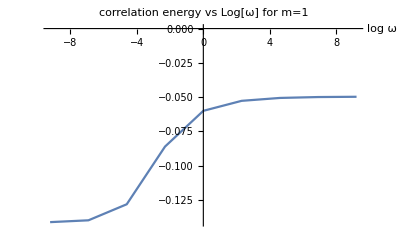

```mathematica
(****************************** CORRELATION ENERGY VS LOG ω *********************************)
ListLinePlot[data1,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=1"]
```

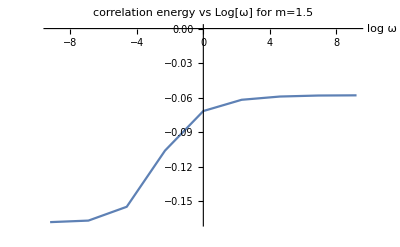

```mathematica
ListLinePlot[data2,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=1.5"]
```

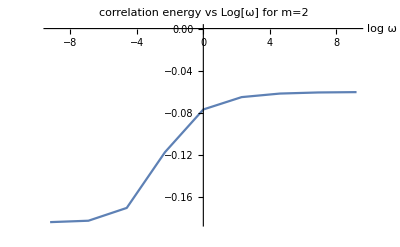

```mathematica
ListLinePlot[data3,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=2"]
```

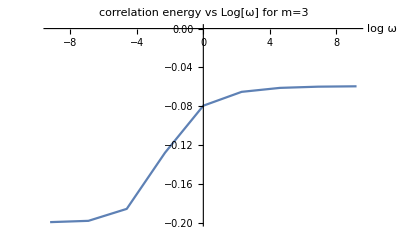

```mathematica
ListLinePlot[data4,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=3"]
```

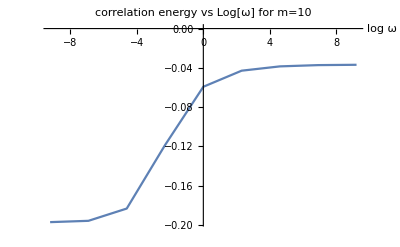

```mathematica
ListLinePlot[data5,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=10"]
```

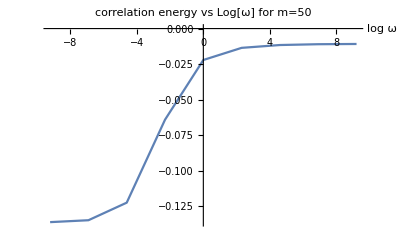

```mathematica
ListLinePlot[data6,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=50"]
```

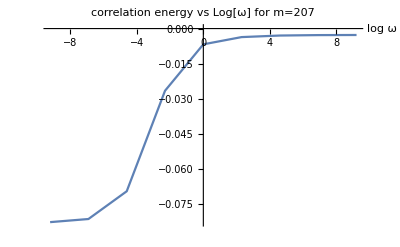

```mathematica
ListLinePlot[data7,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=207"]
```

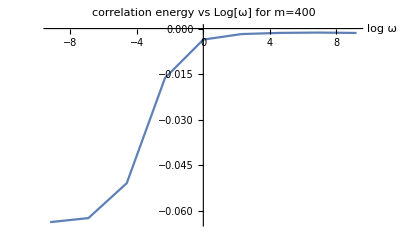

```mathematica
ListLinePlot[data8,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=400"]
```

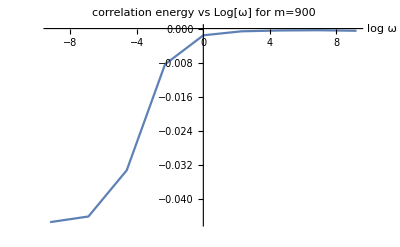

```mathematica
ListLinePlot[data9,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=900"]
```

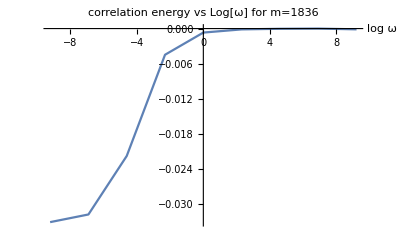

```mathematica
ListLinePlot[data10,PlotRange->All,AxesLabel->{"log ω",""},PlotLabel->"correlation energy vs Log[ω] for m=1836"]
```

## Fit m-included

FittedModel[-0.125954+0.0968198/(1+ⅇ^(-0.900874 («1»)))]

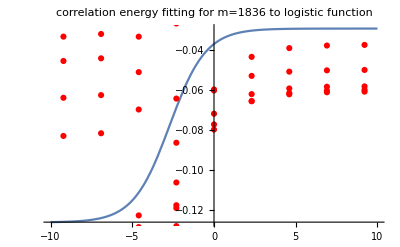

{a→0.0968198,b→-2.71545,c→-0.125954,d→-0.900874}

```mathematica
(****************************** CORRELATION ENERGY FITTING *********************************)
fitM=NonlinearModelFit[dataM,{a/(1+Exp[d*(x-b)])+c},{a,b,c,d},x,Method->NMinimize]
Show[{Plot[fitM[x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[dataM,PlotStyle->Red]}]
fitM["BestFitParameters"]
```

FittedModel[-0.051322-0.0897721/(1+ⅇ^(2.73726+x))]

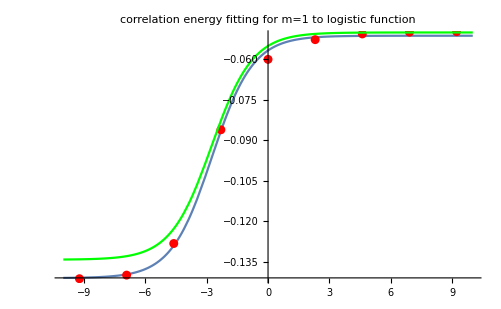

{a→-0.0897721,b→-2.73726,c→-0.051322}

```mathematica
mod[1]=NonlinearModelFit[setM[[1]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[1][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1 to logistic function",Red]],ListPlot[setM[[1]],PlotStyle->Red],Plot[allfuns[[1]],{x,-10,10},PlotStyle->Green]}]
mod[1]["BestFitParameters"]
```

FittedModel[-0.0598535-0.10809/(1+ⅇ^(2.56353+x))]

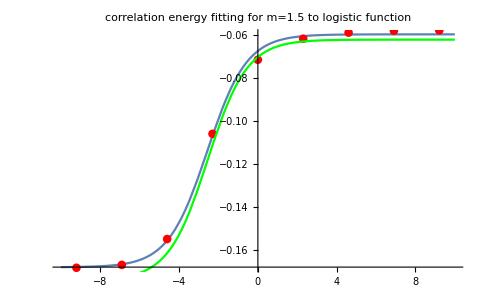

{a→-0.10809,b→-2.56353,c→-0.0598535}

```mathematica
mod[2]=NonlinearModelFit[setM[[2]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[2][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1.5 to logistic function",Red]],ListPlot[setM[[2]],PlotStyle->Red],Plot[allfuns[[2]],{x,-10,10},PlotStyle->Green]}]
mod[2]["BestFitParameters"]
```

FittedModel[-0.0628371-0.120755/(1+ⅇ^(2.45688+x))]

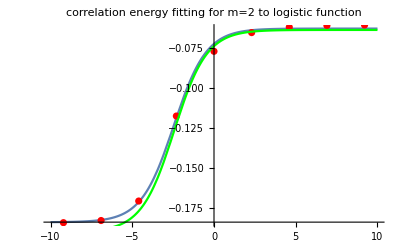

{a→-0.120755,b→-2.45688,c→-0.0628371}

```mathematica
mod[3]=NonlinearModelFit[setM[[3]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[3][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=2 to logistic function",Red]],ListPlot[setM[[3]],PlotStyle->Red],Plot[allfuns[[3]],{x,-10,10},PlotStyle->Green]}]
mod[3]["BestFitParameters"]
```

FittedModel[-0.0622774-0.136713/(1+ⅇ^(2.33885+x))]

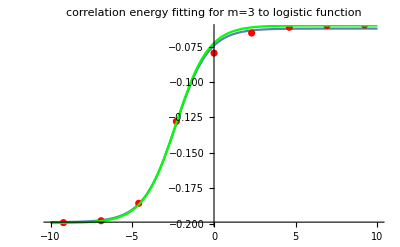

{a→-0.136713,b→-2.33885,c→-0.0622774}

```mathematica
mod[4]=NonlinearModelFit[setM[[4]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[4][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=3 to logistic function",Red]],ListPlot[setM[[4]],PlotStyle->Red],Plot[allfuns[[4]],{x,-10,10},PlotStyle->Green]}]
mod[4]["BestFitParameters"]
```

FittedModel[-0.0396889-0.157558/(1+ⅇ^(2.2501+x))]

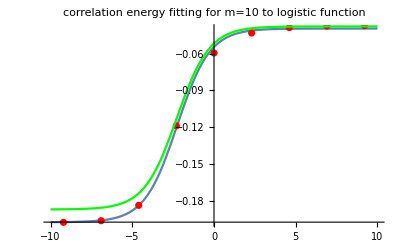

{a→-0.157558,b→-2.2501,c→-0.0396889}

```mathematica
mod[5]=NonlinearModelFit[setM[[5]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[5][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=10 to logistic function",Red]],ListPlot[setM[[5]],PlotStyle->Red],Plot[allfuns[[5]],{x,-10,10},PlotStyle->Green]}]
mod[5]["BestFitParameters"]
```

FittedModel[-0.0121638-0.124472/(1+ⅇ^(2.61124+x))]

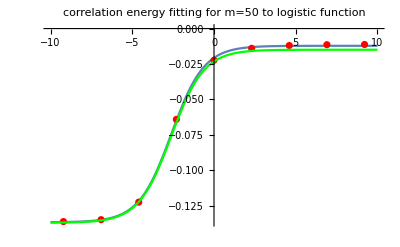

{a→-0.124472,b→-2.61124,c→-0.0121638}

```mathematica
mod[6]=NonlinearModelFit[setM[[6]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[6][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=50 to logistic function",Red]],ListPlot[setM[[6]],PlotStyle->Red],Plot[allfuns[[6]],{x,-10,10},PlotStyle->Green]}]
mod[6]["BestFitParameters"]
```

FittedModel[-0.00330346-0.0801408/(1+ⅇ^(3.14139+x))]

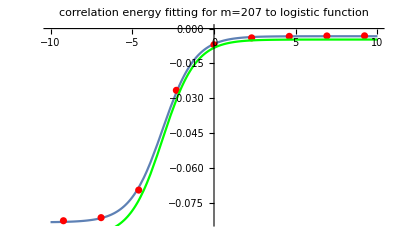

{a→-0.0801408,b→-3.14139,c→-0.00330346}

```mathematica
mod[7]=NonlinearModelFit[setM[[7]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[7][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=207 to logistic function",Red]],ListPlot[setM[[7]],PlotStyle->Red],Plot[allfuns[[7]],{x,-10,10},PlotStyle->Green]}]
mod[7]["BestFitParameters"]
```

FittedModel[-0.00172144-0.0626235/(1+ⅇ^(3.40841+x))]

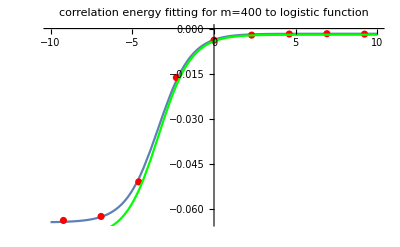

{a→-0.0626235,b→-3.40841,c→-0.00172144}

```mathematica
mod[8]=NonlinearModelFit[setM[[8]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[8][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=400 to logistic function",Red]],ListPlot[setM[[8]],PlotStyle->Red],Plot[allfuns[[8]],{x,-10,10},PlotStyle->Green]}]
mod[8]["BestFitParameters"]
```

FittedModel[-0.00071752-0.0451133/(1+ⅇ^(3.74171+x))]

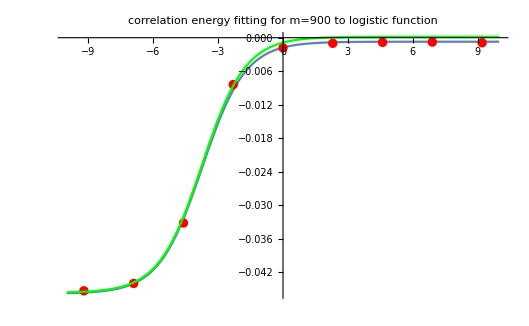

{a→-0.0451133,b→-3.74171,c→-0.00071752}

```mathematica
mod[9]=NonlinearModelFit[setM[[9]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[9][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=900 to logistic function",Red]],ListPlot[setM[[9]],PlotStyle->Red],Plot[allfuns[[9]],{x,-10,10},PlotStyle->Green]}]
mod[9]["BestFitParameters"]
```

FittedModel[-0.0003256-0.0332461/(1+ⅇ^(4.05222+x))]

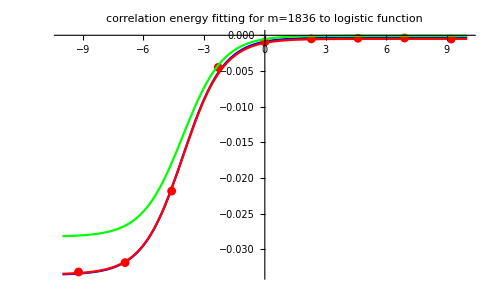

{a→-0.0332461,b→-4.05222,c→-0.0003256}

```mathematica
mod[10]=NonlinearModelFit[setM[[10]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[mod[10][x],{x,-10,10},PlotStyle->Blue,PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setM[[10]],PlotStyle->Red],Plot[allfuns[[10]],{x,-10,10},PlotStyle->Green],Plot[-0.0005-0.033/(1+ⅇ^(4.05+x)),{x,-10,10},PlotStyle->Red,PlotRange->All]}]
mod[10]["BestFitParameters"]
```

```mathematica
Normal[mod[10]]
```

-0.0003256-0.0332461/(1+ⅇ^(4.05222+x))

```mathematica
cps[[10]]
```

{-0.0281591,-4.05771,-0.0000587005}

```mathematica
allfitparamM={{-0.08977206554104032,-2.7372602170552627,-0.051322037836195},{-0.10809018463115107,-2.5635349861001386,-0.05985351592655446},{-0.12075482494963688,-2.4568787450173213,-0.06283713870258262},{-0.13671331036178294,-2.3388502858312776,-0.06227744822678973},{-0.1575576280960951,-2.2501018583405497,-0.03968894157338043},{-0.12447153779843306,-2.6112367624077564,-0.01216375136072869},{-0.08014084248787924,-3.1413874330138163,-0.0033034615478527186},{-0.0626234699497307,-3.408405545299976,-0.0017214383854060441},{-0.045113254905820535,-3.741714591511802,-0.0007175196754938341},{-0.033246122697883934,-4.052217912345134,-0.00032559956472526155}};
cps=Table[{cp1[Log[massP[[i]]]],cp2[Log[massP[[i]]]],cp3[Log[massP[[i]]]]},{i,10}];
(*normalfuns=Table[Normal[mod[i]],{i,10}];*)
fun[a_,b_,c_]:=c+a/(1+ⅇ^(-b+x));
allfuns=Table[fun[cps[[i,1]],cps[[i,2]],cps[[i,3]]],{i,10}];
allfuns2=Table[fun[allfitparamM[[i,1]],allfitparamM[[i,2]],allfitparamM[[i,3]]],{i,10}];
(*For[i=1,i<11,i++,funs[i]=normalfuns[[i]]]*)
allvals=Table[allfuns[[i]]/.x->logo[[j]],{i,10},{j,9}];
allvals2=Table[allfuns2[[i]]/.x->logo[[j]],{i,10},{j,9}];
funsabs=Table[Abs[allvals[[i,j]]-set[i][[j]]],{i,10},{j,9}];
funsper=Table[Abs[allvals[[i,j]]-set[i][[j]]]/(set[i][[j]])*100,{i,10},{j,9}];
funsabs2=Table[Abs[allvals2[[i,j]]-set[i][[j]]],{i,10},{j,9}];
funsper2=Table[Abs[allvals2[[i,j]]-set[i][[j]]]/(set[i][[j]])*100,{i,10},{j,9}];
```

```mathematica
commorse=Table[{allfitparamM[[i,j]],cps[[i,j]]},{i,10},{j,3}];
commorse//TableForm
```

```mathematica
diffmorse=Table[Abs[allfitparamM[[i,j]]-cps[[i,j]]],{i,10},{j,3}];
diffmorse//TableForm
```

## Fit m-excluded

FittedModel[-0.0147678-0.0286483/(1+ⅇ^(2.54319+x))]

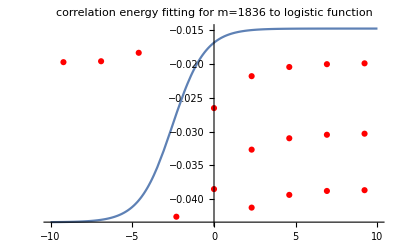

{a→-0.0286483,b→-2.54319,c→-0.0147678}

```mathematica
fitEX=NonlinearModelFit[dataEX,{a/(1+Exp[(x-b)])+c},{a,b,c},x]
Show[{Plot[fitEX[x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[dataEX,PlotStyle->Red]}]
fitEX["BestFitParameters"]
```

FittedModel[-0.051322-0.0897721/(1+ⅇ^(2.73726+x))]

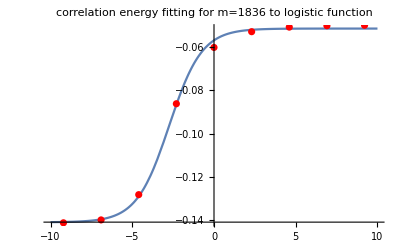

{a→-0.0897721,b→-2.73726,c→-0.051322}

```mathematica
fitex[1]=NonlinearModelFit[setEX[[1]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[1][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[1]],PlotStyle->Red]}]
fitex[1]["BestFitParameters"]
```

FittedModel[-0.0399023-0.0720601/(1+ⅇ^(2.56354+x))]

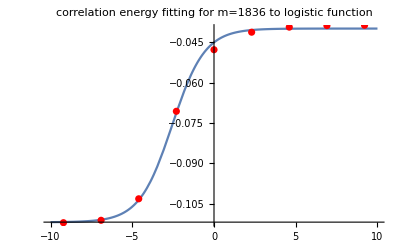

{a→-0.0720601,b→-2.56354,c→-0.0399023}

```mathematica
fitex[2]=NonlinearModelFit[setEX[[2]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[2][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[2]],PlotStyle->Red]}]
fitex[2]["BestFitParameters"]
```

FittedModel[-0.0314186-0.0603774/(1+ⅇ^(2.45688+x))]

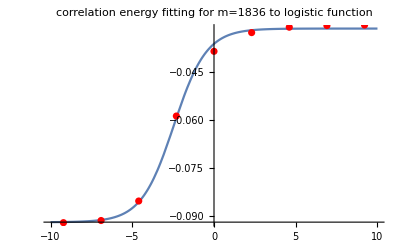

{a→-0.0603774,b→-2.45688,c→-0.0314186}

```mathematica
fitex[3]=NonlinearModelFit[setEX[[3]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[3][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[3]],PlotStyle->Red]}]
fitex[3]["BestFitParameters"]
```

FittedModel[-0.0207592-0.0455711/(1+ⅇ^(2.33885+x))]

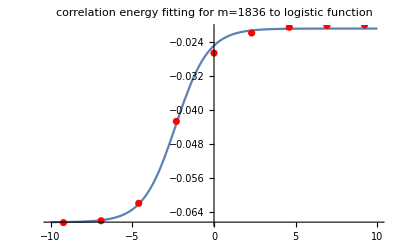

{a→-0.0455711,b→-2.33885,c→-0.0207592}

```mathematica
fitex[4]=NonlinearModelFit[setEX[[4]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[4][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[4]],PlotStyle->Red]}]
fitex[4]["BestFitParameters"]
```

FittedModel[-0.00396891-0.0157558/(1+ⅇ^(2.25011+x))]

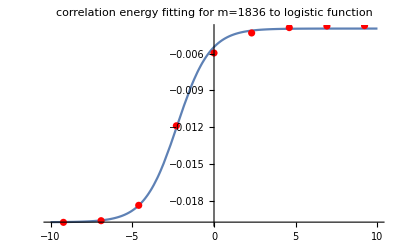

{a→-0.0157558,b→-2.25011,c→-0.00396891}

```mathematica
fitex[5]=NonlinearModelFit[setEX[[5]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[5][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[5]],PlotStyle->Red]}]
fitex[5]["BestFitParameters"]
```

FittedModel[-0.000243285-0.00248943/(1+ⅇ^(2.61126+x))]

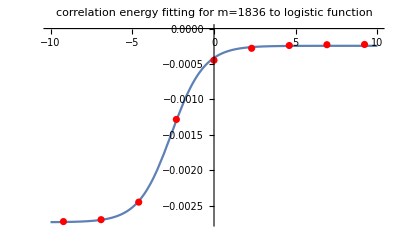

{a→-0.00248943,b→-2.61126,c→-0.000243285}

```mathematica
fitex[6]=NonlinearModelFit[setEX[[6]],{a/(1+Exp[(x-b)])+c},{a,b,c},x,Method->NMinimize]
Show[{Plot[fitex[6][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[6]],PlotStyle->Red]}]
fitex[6]["BestFitParameters"]
```

FittedModel[-0.0000159587-0.000387154/(1+ⅇ^(3.14139+x))]

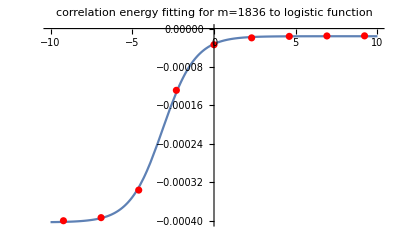

{a→-0.000387154,b→-3.14139,c→-0.0000159587}

```mathematica
fitex[7]=NonlinearModelFit[setEX[[7]],{a/(1+Exp[(x-b)])+c},{a,b,c},x]
Show[{Plot[fitex[7][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[7]],PlotStyle->Red]}]
fitex[7]["BestFitParameters"]
```

FittedModel[-4.30357×10^-6-0.000156559/(1+ⅇ^(3.40841+x))]

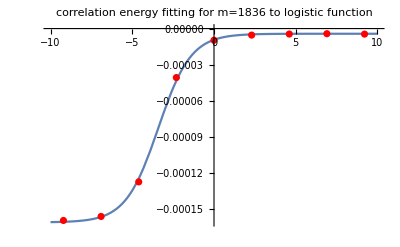

{a→-0.000156559,b→-3.40841,c→-4.30357×10^-6}

```mathematica
fitex[8]=NonlinearModelFit[setEX[[8]],{a/(1+Exp[(x-b)])+c},{a,b,c},x]
Show[{Plot[fitex[8][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[8]],PlotStyle->Red,PlotRange->All]}]
fitex[8]["BestFitParameters"]
```

FittedModel[-7.97235×10^-7-0.0000501258/(1+ⅇ^(3.74171+x))]

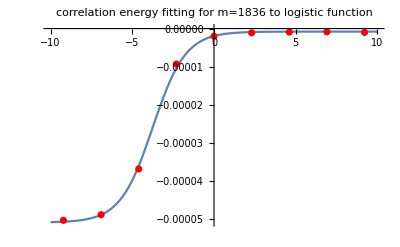

{a→-0.0000501258,b→-3.74171,c→-7.97235×10^-7}

```mathematica
fitex[9]=NonlinearModelFit[setEX[[9]],{a/(1+Exp[(x-b)])+c},{a,b,c},x]
Show[{Plot[fitex[9][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[9]],PlotStyle->Red]}]
fitex[9]["BestFitParameters"]
```

FittedModel[-1.77336×10^-7-0.0000181079/(1+ⅇ^(4.05222+x))]

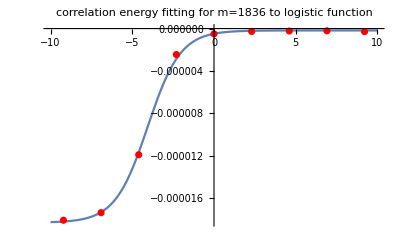

{a→-0.0000181079,b→-4.05222,c→-1.77336×10^-7}

```mathematica
fitex[10]=NonlinearModelFit[setEX[[10]],{a/(1+Exp[(x-b)])+c},{a,b,c},x]
Show[{Plot[fitex[10][x],{x,-10,10},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[setEX[[10]],PlotStyle->Red]}]
fitex[10]["BestFitParameters"]
```

## Results

```mathematica
(**************************** Fitting Parameters *********************************)
(* General form of Logistic function : a/(1+Exp[(x-b)])+c ---- here x is Log[ω]*)
For[i=1,i<11,i++,fitparamM[i]=Table[mod[i]["BestFitParameters"][[j]][[2]],{j,3}]];
allfitparamM=Table[fitparamM[i],{i,10}];
```

```mathematica
allfitparamM={{-0.08977206554104032,-2.7372602170552627,-0.051322037836195},{-0.10809018463115107,-2.5635349861001386,-0.05985351592655446},{-0.12075482494963688,-2.4568787450173213,-0.06283713870258262},{-0.13671331036178294,-2.3388502858312776,-0.06227744822678973},{-0.1575576280960951,-2.2501018583405497,-0.03968894157338043},{-0.12447153779843306,-2.6112367624077564,-0.01216375136072869},{-0.08014084248787924,-3.1413874330138163,-0.0033034615478527186},{-0.0626234699497307,-3.408405545299976,-0.0017214383854060441},{-0.045113254905820535,-3.741714591511802,-0.0007175196754938341},{-0.033246122697883934,-4.052217912345134,-0.00032559956472526155}};
```

```mathematica
Labeled[TableForm[allfitparamM,TableHeadings->{{"m=1","m=1.5","m=2","m=3","m=10","m=50","m=207","m=400","m-900","m=1836"},{ "a","b","c"}}],Framed[Style["Table of fitting m-included parameters for different masses",Red,Bold,15]],Top]
```

| a | b | c
m=1 | -0.0897721 | -2.73726 | -0.051322
m=1.5 | -0.10809 | -2.56353 | -0.0598535
m=2 | -0.120755 | -2.45688 | -0.0628371
m=3 | -0.136713 | -2.33885 | -0.0622774
m=10 | -0.157558 | -2.2501 | -0.0396889
m=50 | -0.124472 | -2.61124 | -0.0121638
m=207 | -0.0801408 | -3.14139 | -0.00330346
m=400 | -0.0626235 | -3.40841 | -0.00172144
m-900 | -0.0451133 | -3.74171 | -0.00071752
m=1836 | -0.0332461 | -4.05222 | -0.0003256Table of fitting m-included parameters for different masses

```mathematica
aparam=Table[{Log[massP[[i]]],allfitparamM[[i,1]]},{i,10}];
bparam=Table[{Log[massP[[i]]],allfitparamM[[i,2]]},{i,10}];
cparam=Table[{Log[massP[[i]]],allfitparamM[[i,3]]},{i,10}];

(* general formula *)
(*cp1[mp_]:=-0.14994494068743744+0.2696499706343979 (1-ⅇ^(-0.20175328107934945 (-1.989394285552385+mp)))^2;
cp2[mp_]:=-2.257179800358067-6.822991274643732 (1-ⅇ^(-0.12783915985100308 (-1.8759451164060055+mp)))^2;*)
(*cp3[mp_]:=-0.06203650871413124+0.06261323655976184 (1-ⅇ^(-0.8609559440418215 (-0.5778165619886467+mp)))^4;*)
(*cp1[mp_]:=-0.08937934643108923-0.047169832887953796 mp-0.0024362296514053887 mp^2+0.0069753962262640475 mp^3-0.0012474299239326526 mp^4+0.00006536659132833754 mp^5;
cp2[mp_]:=-2.7395037624507257+0.4837407866416987 mp-0.09405717773653584 mp^2-0.020257817992589144 mp^3+0.004895499383304689 mp^4-0.00027758585343464956 mp^5;
cp3[mp_]:=-0.050871705934566705-0.03627331566694035 mp+0.03217580482223547 mp^2-0.008001820161621253 mp^3+0.0008409414499977088 mp^4-0.00003254300741888807 mp^5;*)
(*cp3[mp_]:=-0.06374755957571915+0.06771370922824817 (1-ⅇ^(-0.5781358833661908 (-0.6412381270577683+mp)))^2*)


cp1[x_]:=-0.08990402199175584-0.04001745026785101 x-0.015228861805657388 x^2+0.014712738775446097 x^3-0.003297913723172049 x^4+0.0003122459729133951 x^5-0.000011061244703704963 x^6;
cp2[x_]:=-2.7376897403429674+0.4590120186778304 x-0.04982771617214953 x^2-0.047009036253468736 x^3+0.011984876557079926 x^4-0.0011311507794945815 x^5+0.00003824333347333787 x^6;
cp3[x_]:=-0.05103441547156189-0.03405525759110216 x+0.028208623175490357 x^2-0.005602357487671382 x^3+0.00020505654396696586 x^4+0.00004401788636548901 x^5-3.430253168353952*^-6 x^6;

corrfit[x_,mp_]:=cp1[mp]/(1+Exp[(x-cp2[mp])])+cp3[mp];
corrfitdata=Table[corrfit[logo[[j]],Log[massP[[i]]]],{i,10},{j,9}];
corrfitabserror=Table[Abs[corrfitdata[[i,j]]-set[i][[j]]],{i,10},{j,9}];
corrfitpererror=Table[Abs[corrfitdata[[i,j]]-set[i][[j]]]/(set[i][[j]])*100,{i,10},{j,9}];
```

```mathematica
corrfitpererror//TableForm
```

-0.380128 | -0.311097 | -0.477236 | -0.230303 | -5.93798 | -2.18972 | -0.873768 | -2.08455 | -2.47168
-0.0104932 | -0.0464431 | -0.705247 | -1.38073 | -4.70842 | -0.777531 | -2.71197 | -4.12297 | -4.41881
-0.177088 | -0.132233 | -0.405896 | -1.08491 | -5.95433 | -2.18337 | -1.63741 | -3.2173 | -3.73988
-0.445995 | -0.412807 | -0.00579121 | -0.717542 | -7.64043 | -4.0483 | -0.395852 | -2.28799 | -2.90685
-0.00223107 | -0.00798887 | -0.203038 | -1.78867 | -7.33296 | -3.33747 | -3.71964 | -6.8919 | -7.76344
-0.154115 | -0.0318711 | -0.701605 | -0.895394 | -8.53426 | -7.93488 | -0.356049 | -4.63988 | -6.03913
-0.433377 | -0.0802467 | -1.87399 | -3.07806 | -5.44937 | -9.51077 | -1.54887 | -3.23647 | -4.4537
-1.15971 | -0.676892 | -1.5402 | -8.08843 | -3.49029 | -1.25539 | -10.7682 | -16.7647 | -8.02322
-0.322327 | -0.386916 | -2.7787 | -9.28107 | -14.2986 | -38.2184 | -37.5846 | -34.1643 | -43.7067
-0.792497 | -0.130774 | -1.58636 | -17.9613 | -2.91998 | -12.65 | -8.59751 | -1.16388 | -27.8939

-4.29049 | -4.21956 | -3.39622 | -2.63588 | -6.35742 | -1.91167 | -1.24835 | -2.47269 | -2.86221
-3.19875 | -3.26417 | -3.99709 | -4.70846 | -2.18381 | -1.59006 | -5.1288 | -6.56946 | -6.8719
-2.11341 | -2.15844 | -2.68857 | -2.8124 | -6.34905 | -3.41525 | -0.248794 | -1.79578 | -2.31002
-0.522632 | -0.556485 | -0.977553 | -1.49281 | -7.87788 | -4.75669 | -0.409949 | -1.4602 | -2.07337
-4.5267 | -4.53312 | -4.449 | -3.14681 | -10.1871 | -4.92274 | -2.25301 | -5.40592 | -6.26792
-1.32321 | -1.44168 | -2.13973 | -0.135767 | -7.00468 | -4.14621 | -4.93569 | -9.46584 | -10.9348
-6.74918 | -6.40422 | -4.56792 | -10.5784 | -1.40039 | -3.33369 | -5.0803 | -10.1772 | -11.4751
-7.90968 | -7.40109 | -5.05055 | -14.2526 | -1.81881 | -8.43949 | -1.65358 | -3.45852 | -4.30662
-2.05797 | -1.32566 | -1.1636 | -11.4939 | -9.09203 | -29.7992 | -27.6379 | -23.4887 | -34.5623
-15.3952 | -16.2332 | -17.9895 | -6.35337 | -41.6657 | -78.5829 | -84.9365 | -84.6267 | -88.8521

## fitting inner parameters

FittedModel[-0.149945+0.26965 (1-ⅇ^(-0.201753 «1»))^2]

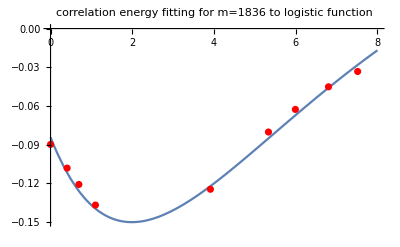

{a→0.26965,b→0.201753,c→1.98939,d→-0.149945}

```mathematica
mod[11]=NonlinearModelFit[aparam,{a*(1-Exp[-b(x-c)])^2+d},{a,b,c,d},x,Method->"Newton"]
Show[{Plot[mod[11][x],{x,0,8},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[aparam,PlotStyle->Red],Graphics[Green,Thickness[0.006],Line[{{#[[1]],cp1[#[[1]]]},#}]&/@aparam]}]
mod[11]["BestFitParameters"]
```

```mathematica
Normal[mod[11]]
```

-0.149945+0.26965 (1-ⅇ^(-0.201753 (-1.98939+x)))^2

FittedModel[-2.25718-6.82299 (1-ⅇ^(-0.127839 «1»))^2]

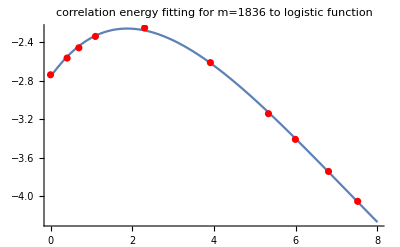

{a→-6.82299,b→0.127839,c→1.87595,d→-2.25718}

```mathematica
mod[12]=NonlinearModelFit[bparam,{a*(1-Exp[-b(x-c)])^2+d},{a,b,c,d},x,Method->NMinimize]
Show[{Plot[mod[12][x],{x,0,8},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[bparam,PlotStyle->Red]}]
mod[12]["BestFitParameters"]
```

```mathematica
Normal[mod[12]]
```

-2.25718-6.82299 (1-ⅇ^(-0.127839 (-1.87595+x)))^2

FittedModel[-0.0620365+0.0626132 (1-ⅇ^(-0.860956 «1»))^4]

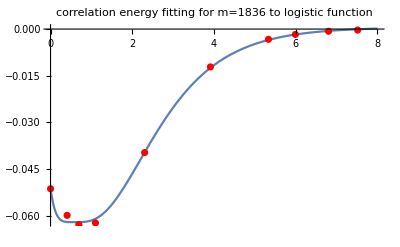

{a→0.0626132,b→0.860956,c→0.577817,d→-0.0620365}

```mathematica
mod[13]=NonlinearModelFit[cparam,{a*(1-Exp[-b(x-c)])^4+d},{a,b,c,d},x,Method->NMinimize]
Show[{Plot[mod[13][x],{x,0,8},PlotLabel->Style["correlation energy fitting for m=1836 to logistic function",Red]],ListPlot[cparam,PlotStyle->Red]}]
mod[13]["BestFitParameters"]
```

```mathematica
Normal[mod[13]]
```

-0.0620365+0.0626132 (1-ⅇ^(-0.860956 (-0.577817+x)))^4

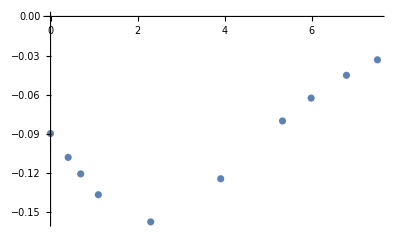

```mathematica
ListPlot[aparam]
```

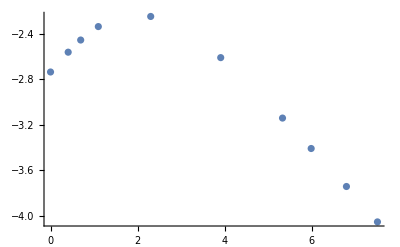

```mathematica
ListPlot[bparam]
```

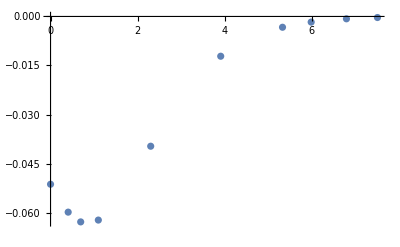

```mathematica
ListPlot[cparam]
```

## EX

```mathematica
For[i=1,i<11,i++,fitparam[i]=Table[fitex[i]["BestFitParameters"][[j]][[2]],{j,3}]]
```

```mathematica
allfitparam=Table[fitparam[i],{i,10}];
```

```mathematica
Labeled[TableForm[allfitparam,TableHeadings->{{"m=1","m=1.5","m=2","m=3","m=10","m=50","m=207","m=400","m-900","m=1836"},{ "a","b","c"}}],Framed[Style["Table of fitting m-excluded parameters for different masses",Red,Bold,15]],Top]
```

| a | b | c
m=1 | -0.0897721 | -2.73726 | -0.051322
m=1.5 | -0.0720601 | -2.56354 | -0.0399023
m=2 | -0.0603774 | -2.45688 | -0.0314186
m=3 | -0.0455711 | -2.33885 | -0.0207592
m=10 | -0.0157558 | -2.25011 | -0.00396891
m=50 | -0.00248943 | -2.61126 | -0.000243285
m=207 | -0.000387154 | -3.14139 | -0.0000159587
m=400 | -0.000156559 | -3.40841 | -4.30357×10^-6
m-900 | -0.0000501258 | -3.74171 | -7.97235×10^-7
m=1836 | -0.0000181079 | -4.05222 | -1.77336×10^-7Table of fitting m-excluded parameters for different masses

```mathematica
Labeled[TableForm[{set[1],set[2],set[3],set[4],set[5],set[6],set[7],set[8],set[9],set[10]},TableHeadings->{{"m=1","m=1.5","m=2","m=3","m=10","m=50","m=207","m=400","m-900","m=1836"}, {"ω=0.0001","ω=0.001","ω=0.01","ω=0.1","ω=1","ω=10","ω=100","ω=1000","ω=10000"}}],Framed[Style["Table of correlation energies for different masses",Red,Bold,15]],Top]
```

| ω=0.0001 | ω=0.001 | ω=0.01 | ω=0.1 | ω=1 | ω=10 | ω=100 | ω=1000 | ω=10000
m=1 | -0.141337 | -0.140006 | -0.128294 | -0.08616 | -0.060066 | -0.052768 | -0.05065 | -0.049998 | -0.049804
m=1.5 | -0.168189 | -0.166854 | -0.15485 | -0.106014 | -0.071659 | -0.061878 | -0.059054 | -0.058182 | -0.05801
m=2 | -0.183855 | -0.182519 | -0.170363 | -0.117372 | -0.077021 | -0.065352 | -0.061987 | -0.060948 | -0.060632
m=3 | -0.199277 | -0.197939 | -0.185627 | -0.127794 | -0.079589 | -0.065423 | -0.061356 | -0.060105 | -0.059732
m=10 | -0.197347 | -0.196007 | -0.183502 | -0.118805 | -0.059557 | -0.043268 | -0.038901 | -0.037607 | -0.037289
m=50 | -0.136159 | -0.134821 | -0.12246 | -0.064103 | -0.022337 | -0.013917 | -0.011953 | -0.011385 | -0.011227
m=207 | -0.08276 | -0.081427 | -0.06956 | -0.026594 | -0.006969 | -0.004001 | -0.003363 | -0.003177 | -0.003137
m=400 | -0.063705 | -0.062375 | -0.050894 | -0.016263 | -0.00386 | -0.002165 | -0.001811 | -0.001702 | -0.001838
m-900 | -0.04532 | -0.043998 | -0.03318 | -0.008381 | -0.001815 | -0.000999 | -0.000835 | -0.000777 | -0.000907
m=1836 | -0.033161 | -0.031848 | -0.021825 | -0.004495 | -0.000921 | -0.000501 | -0.000422 | -0.000385 | -0.000527Table of correlation energies for different masses

## Errors

```mathematica
(**************************** Percentage Error *********************************)
logfun[x_]:=a/(1+Exp[(x-b)])+c;
```

```mathematica
m1Points=Table[logfun[x]/.mod1["BestFitParameters"],{x,set00}];
m32Points=Table[logfun[x]/.mod2["BestFitParameters"],{x,set00}];
m2Points=Table[logfun[x]/.mod3["BestFitParameters"],{x,set00}];
m3Points=Table[logfun[x]/.mod4["BestFitParameters"],{x,set00}];
m10Points=Table[logfun[x]/.mod5["BestFitParameters"],{x,set00}];
m50Points=Table[logfun[x]/.mod6["BestFitParameters"],{x,set00}];
m207Points=Table[logfun[x]/.mod7["BestFitParameters"],{x,set00}];
m400Points=Table[logfun[x]/.mod8["BestFitParameters"],{x,set00}];
m900Points=Table[logfun[x]/.mod9["BestFitParameters"],{x,set00}];
m1836Points=Table[logfun[x]/.mod10["BestFitParameters"],{x,set00}];
```

```mathematica
m1Error=Table[Abs[(m1Points[[i]]-set1[[i]])/set1[[i]]]*100,{i,1,9}];
m32Error=Table[Abs[(m32Points[[i]]-set1[[i]])/set1[[i]]]*100,{i,1,9}];
m2Error=Table[Abs[(m2Points[[i]]-set1[[i]])/set1[[i]]]*100,{i,1,9}];
m3Error=Table[Abs[(m3Points[[i]]-set1[[i]])/set1[[i]]]*100,{i,1,9}];
m10Error=Table[Abs[(m10Points[[i]]-set2[[i]])/set2[[i]]]*100,{i,1,9}];
m50Error=Table[Abs[(m50Points[[i]]-set3[[i]])/set3[[i]]]*100,{i,1,9}];
m207Error=Table[Abs[(m207Points[[i]]-set4[[i]])/set4[[i]]]*100,{i,1,9}];
m400Error=Table[Abs[(m400Points[[i]]-set5[[i]])/set5[[i]]]*100,{i,1,9}];
m900Error=Table[Abs[(m900Points[[i]]-set6[[i]])/set6[[i]]]*100,{i,1,9}];
m1836Error=Table[Abs[(m1836Points[[i]]-set7[[i]])/set7[[i]]]*100,{i,1,9}];

m1ABSError=Table[Abs[m1Points[[i]]-set1[[i]]],{i,1,9}];
m32ABSError=Table[Abs[m32Points[[i]]-set1[[i]]],{i,1,9}];
m2ABSError=Table[Abs[m2Points[[i]]-set1[[i]]],{i,1,9}];
m3ABSError=Table[Abs[m3Points[[i]]-set1[[i]]],{i,1,9}];
m10ABSError=Table[Abs[m10Points[[i]]-set2[[i]]],{i,1,9}];
m50ABSError=Table[Abs[m50Points[[i]]-set3[[i]]],{i,1,9}];
m207ABSError=Table[Abs[m207Points[[i]]-set4[[i]]],{i,1,9}];
m400ABSError=Table[Abs[m400Points[[i]]-set5[[i]]],{i,1,9}];
m900ABSError=Table[Abs[m900Points[[i]]-set6[[i]]],{i,1,9}];
m1836ABSError=Table[Abs[m1836Points[[i]]-set7[[i]]],{i,1,9}];
```

```mathematica
Labeled[TableForm[{m1Error,m32Error,m2Error,m3Error,m10Error,m50Error,m207Error,m400Error,m900Error,m1836Error},TableHeadings->{{"m=1","m=1.5","m=2","m=3","m=10","m=50","m=207","m=400","m=900","m=1836"}, {"ω=0.0001","ω=0.001","ω=0.01","ω=0.1","ω=1","ω=10","ω=100","ω=1000","ω=10000"}}],Framed[Style["Table of percentage error of fitting points for different masses",Red,Bold,15]],Top]
```

| ω=0.0001 | ω=0.001 | ω=0.01 | ω=0.1 | ω=1 | ω=10 | ω=100 | ω=1000 | ω=10000
m=1 | 0.275062 | 0.201286 | 0.627127 | 0.514603 | 5.49985 | 1.6559 | 1.45173 | 2.67424 | 3.07345
m=1.5 | 18.7202 | 18.9616 | 21.236 | 24.0696 | 12.4888 | 14.9734 | 18.3357 | 19.7336 | 20.1963
m=2 | 29.7911 | 30.1327 | 33.2785 | 37.6335 | 20.4486 | 20.9818 | 24.2393 | 25.6777 | 26.1605
m=3 | 40.6852 | 41.1236 | 45.1044 | 50.2125 | 23.6444 | 20.392 | 23.1233 | 24.4957 | 24.9685
m=10 | 17.1817 | 17.323 | 18.5714 | 13.72 | 23.8257 | 33.5068 | 32.8299 | 32.0785 | 31.8988
m=50 | 25.7837 | 26.0605 | 28.5347 | 44.7297 | 73.4607 | 80.4721 | 80.738 | 80.5454 | 80.4557
m=207 | 58.2316 | 58.7648 | 63.1255 | 78.5259 | 92.0432 | 94.9441 | 95.1226 | 95.0736 | 95.0475
m=400 | 67.5047 | 68.1146 | 72.8127 | 85.5123 | 94.2449 | 96.3266 | 96.4008 | 96.3272 | 96.2998
m=900 | 66.5008 | 67.3646 | 73.4331 | 85.5888 | 93.4533 | 96.4491 | 96.6925 | 96.6127 | 96.5694
m=1836 | 59.6993 | 60.9908 | 69.0719 | 80.8831 | 91.4102 | 98.6733 | 100.189 | 100.395 | 100.421Table of percentage error of fitting points for different masses

```mathematica
Labeled[TableForm[{m1ABSError,m32ABSError,m2ABSError,m3ABSError,m10ABSError,m50ABSError,m207ABSError,m400ABSError,m900ABSError,m1836ABSError},TableHeadings->{{"m=1","m=1.5","m=2","m=3","m=10","m=50","m=207","m=400","m=900","m=1836"}, {"ω=0.0001","ω=0.001","ω=0.01","ω=0.1","ω=1","ω=10","ω=100","ω=1000","ω=10000"}}],Framed[Style["Table of Absolute error of fitting points for different masses",Red,Bold,15]],Top]
```

| ω=0.0001 | ω=0.001 | ω=0.01 | ω=0.1 | ω=1 | ω=10 | ω=100 | ω=1000 | ω=10000
m=1 | 0.000388764 | 0.000281813 | 0.000804566 | 0.000443264 | 0.0032954 | 0.000870691 | 0.00073247 | 0.00133185 | 0.00152458
m=1.5 | 0.0264586 | 0.0265473 | 0.0272446 | 0.0207328 | 0.00748303 | 0.00787315 | 0.00925129 | 0.00982793 | 0.0100184
m=2 | 0.0421059 | 0.0421876 | 0.0426943 | 0.0324163 | 0.0122524 | 0.0110325 | 0.0122299 | 0.0127883 | 0.0129769
m=3 | 0.0575032 | 0.0575755 | 0.0578663 | 0.0432515 | 0.0141672 | 0.0107223 | 0.0116668 | 0.0121996 | 0.0123856
m=10 | 0.0288977 | 0.0289041 | 0.0287577 | 0.0145424 | 0.017033 | 0.0206586 | 0.0193106 | 0.0185888 | 0.0184289
m=50 | 0.0474046 | 0.0475654 | 0.0486125 | 0.052492 | 0.0564465 | 0.0523921 | 0.0498372 | 0.0488822 | 0.0485695
m=207 | 0.116042 | 0.116319 | 0.117178 | 0.10034 | 0.0730749 | 0.0618532 | 0.0580857 | 0.0568673 | 0.0564915
m=400 | 0.133219 | 0.133509 | 0.133613 | 0.101584 | 0.0559193 | 0.0413607 | 0.0371606 | 0.0358876 | 0.0355625
m=900 | 0.0905468 | 0.0908216 | 0.0899262 | 0.0548564 | 0.0206569 | 0.0130814 | 0.0111893 | 0.0106342 | 0.0104672
m=1836 | 0.0494071 | 0.0496629 | 0.0480464 | 0.021502 | 0.00615465 | 0.00359368 | 0.00298262 | 0.00280403 | 0.00275857Table of Absolute error of fitting points for different masses

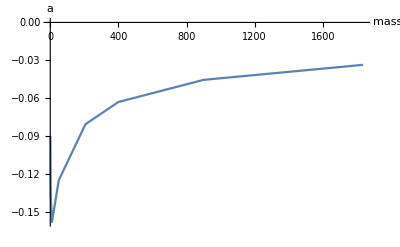

```mathematica
(**************************** Plotting fitting parameters vs mass *********************************)
apar={m1[[1]],m32[[1]],m2[[1]],m3[[1]],m10[[1]],m50[[1]],m207[[1]],m400[[1]],m900[[1]],m1836[[1]]};
bpar={m1[[2]],m32[[2]],m2[[2]],m3[[2]],m10[[2]],m50[[2]],m207[[2]],m400[[2]],m900[[2]],m1836[[2]]};
cpar={m1[[3]],m32[[3]],m2[[3]],m3[[3]],m10[[2]],m50[[3]],m207[[3]],m400[[3]],m900[[3]],m1836[[3]]};
mass={1,1.5,2,3,10,50,207,400,900,1836};

ListLinePlot[Transpose[{mass,apar}],AxesLabel->{Style["mass",Red,Bold],Style["a",Red,Bold,18]}]
```

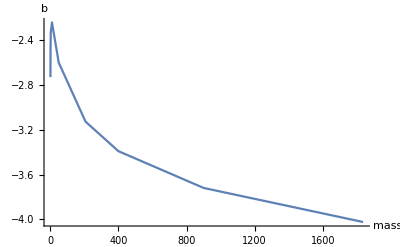

```mathematica
ListLinePlot[Transpose[{mass,bpar}],AxesLabel->{Style["mass",Red,Bold],Style["b",Red,Bold,18]}]
```

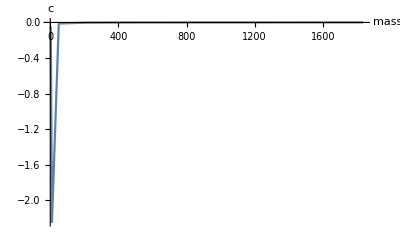

```mathematica
ListLinePlot[Transpose[{mass,cpar}],AxesLabel->{Style["mass",Red,Bold],Style["c",Red,Bold,18]},PlotRange->All]
```

## one step fitting

```mathematica
For[i=11,i<14,i++,fitparamin[i]=Table[mod[i]["BestFitParameters"][[j]][[2]],{j,4}]];
allfitparamin=Table[fitparamin[i],{i,11,13}];
```

```mathematica
allfitparamin={{0.2696499706343979,0.20175328107934945,1.989394285552385,-0.14994494068743744},{-6.822991274643732,0.12783915985100308,1.8759451164060055,-2.257179800358067},{0.06771370922824817,0.5781358833661908,0.6412381270577683,-0.06374755957571915}};
```

```mathematica
cp1p=d1+a1 (1-ⅇ^(-b1 (-c1+mp)))^2;
cp2p=d2+a2 (1-ⅇ^(-b2 (-c2+mp)))^2;
cp3p=d3+a3 (1-ⅇ^(-b3(-c3+mp)))^2;
model=cp1p/(1+Exp[(ω-cp2p)])+cp3p;

fitall=NonlinearModelFit[set3f,model,{a1,b1,c1,d1,a2,b2,c2,d2,a3,b3,c3,d3},{ω,mp}]
fitall["BestFitParameters"]
```

FittedModel[-0.0618041+0.0682253 (1-ⅇ^(-0.504882 (-«19»+mp)))^2+(-0.150416+0.230828 (1-ⅇ^(-0.226486 «1»))^2)/(1+ⅇ^(2.17333+4.23313 (1-ⅇ^(«1»))^2+ω))]

{a1→0.230828,b1→0.226486,c1→1.91208,d1→-0.150416,a2→-4.23313,b2→0.196774,c2→1.78659,d2→-2.17333,a3→0.0682253,b3→0.504882,c3→0.606631,d3→-0.0618041}

```mathematica
Show[{Plot3D[fitall[ω,mp],{ω,-10,10},{mp,0,8},PlotStyle->Opacity[.2]],Graphics3D[{Red,Point[set3f]}]}]
```

-Graphics3D-

```mathematica
fitall["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.230828 | 0.0199499 | 11.5704 | 1.33574×10^-18
b1 | 0.226486 | 0.0153052 | 14.7979 | 2.36659×10^-24
c1 | 1.91208 | 0.0506405 | 37.7578 | 7.05823×10^-52
d1 | -0.150416 | 0.00191178 | -78.6782 | 4.57182×10^-76
a2 | -4.23313 | 2.47004 | -1.71379 | 0.0905389
b2 | 0.196774 | 0.0785492 | 2.50511 | 0.0143256
c2 | 1.78659 | 0.200332 | 8.91815 | 1.55561×10^-13
d2 | -2.17333 | 0.0812828 | -26.7378 | 4.99242×10^-41
a3 | 0.0682253 | 0.00181245 | 37.6427 | 8.84844×10^-52
b3 | 0.504882 | 0.0294001 | 17.1728 | 3.18682×10^-28
c3 | 0.606631 | 0.0442585 | 13.7066 | 1.80839×10^-22
d3 | -0.0618041 | 0.00107137 | -57.6871 | 9.87481×10^-66

```mathematica
flatp=FlattenAt[allfitparamin,{{1},{2},{3}}];
```

```mathematica
TableForm[Transpose[{fitall["BestFitParameters"],flatp}],TableHeadings->{{""},{"1 step fit","3 step fit"}}]
```

| 1 step fit | 3 step fit
 | a1→0.230828 | 0.26965
 | b1→0.226486 | 0.201753
 | c1→1.91208 | 1.98939
 | d1→-0.150416 | -0.149945
 | a2→-4.23313 | -6.82299
 | b2→0.196774 | 0.127839
 | c2→1.78659 | 1.87595
 | d2→-2.17333 | -2.25718
 | a3→0.0682253 | 0.0677137
 | b3→0.504882 | 0.578136
 | c3→0.606631 | 0.641238
 | d3→-0.0618041 | -0.0637476

```mathematica
Normal[fitall]
```

-0.0618041+0.0682253 (1-ⅇ^(-0.504882 (-0.606631+mp)))^2+(-0.150416+0.230828 (1-ⅇ^(-0.226486 (-1.91208+mp)))^2)/(1+ⅇ^(2.17333+4.23313 (1-ⅇ^(-0.196774 (-1.78659+mp)))^2+ω))

```mathematica
onefit[ω_,mp_]:=-0.061804116780373064+0.0682253213130882 (1-ⅇ^(-0.5048822928108331 (-0.6066308168335751+mp)))^2+(-0.1504157125006768+0.23082798015101832 (1-ⅇ^(-0.22648565081199984 (-1.9120761177968684+mp)))^2)/(1+ⅇ^(2.1733268673739627+4.233127621761927 (1-ⅇ^(-0.19677417181445436 (-1.7865931084058364+mp)))^2+ω));
```

```mathematica
onefitdata=Table[onefit[logo[[j]],Log[massP[[i]]]],{i,10},{j,9}];
```

```mathematica
onefitabserror=Table[Abs[onefitdata[[i,j]]-set[i][[j]]],{i,10},{j,9}];
onefitpererror=Table[Abs[onefitdata[[i,j]]-set[i][[j]]]/(set[i][[j]])*100,{i,10},{j,9}];
```

```mathematica
onefitabserror//TableForm
```

0.00583261 | 0.00585873 | 0.00560825 | 0.00425788 | 0.00281411 | 0.000715718 | 0.00243688 | 0.00304899 | 0.003239
0.00492771 | 0.00494069 | 0.0052586 | 0.00322695 | 0.00277375 | 0.0000146005 | 0.0020549 | 0.00285089 | 0.00301528
0.00476439 | 0.0048333 | 0.00558334 | 0.00420861 | 0.00493801 | 0.00254942 | 0.000194303 | 0.000742817 | 0.00104862
0.0000601891 | 0.000192329 | 0.00149189 | 0.00261396 | 0.00779277 | 0.00546685 | 0.00270577 | 0.00158671 | 0.00122691
0.00949362 | 0.0093653 | 0.00797236 | 0.00185929 | 0.00566048 | 0.00243082 | 0.000488969 | 0.00163668 | 0.00194004
0.0003294 | 0.000138254 | 0.00088563 | 0.00184495 | 0.00230891 | 0.00378048 | 0.00500193 | 0.00549517 | 0.00564569
0.00589356 | 0.00536184 | 0.00234081 | 0.00238121 | 0.00171965 | 0.00187662 | 0.00222264 | 0.00237933 | 0.0024164
0.0048278 | 0.00422005 | 0.00114715 | 0.00126874 | 0.00034397 | 0.000314553 | 0.00049103 | 0.000582226 | 0.000444445
0.000794216 | 0.000249729 | 0.00173352 | 0.000651985 | 0.00140274 | 0.00147391 | 0.00140052 | 0.0013516 | 0.00148251
0.00454583 | 0.00482932 | 0.00479262 | 0.0024173 | 0.00273288 | 0.00276502 | 0.00273197 | 0.00269957 | 0.00284204

```mathematica
corrfitabserror//TableForm
```

0.00718331 | 0.00702689 | 0.00547641 | 0.00339033 | 0.00493791 | 0.00212801 | 0.00048697 | 0.000117035 | 0.000306232
0.00568789 | 0.00575435 | 0.00649745 | 0.00529958 | 0.00125694 | 0.00129185 | 0.00333671 | 0.0041302 | 0.00429434
0.00554247 | 0.00559643 | 0.0062372 | 0.00495783 | 0.00323324 | 0.00057507 | 0.00181108 | 0.00275135 | 0.00305747
0.000164236 | 0.000224251 | 0.000937352 | 0.00103047 | 0.00714718 | 0.00398922 | 0.00112878 | 4.06806×10^-7 | 0.000361213
0.0106128 | 0.0105647 | 0.00984346 | 0.00541803 | 0.00774658 | 0.00380944 | 0.000803024 | 0.000353535 | 0.000657777
0.000675648 | 0.000533628 | 0.000143003 | 0.00239028 | 0.000912677 | 0.00190029 | 0.00306728 | 0.003555 | 0.00370496
0.00681457 | 0.0064437 | 0.00440638 | 0.00404217 | 0.00132653 | 0.00109556 | 0.00139979 | 0.00155227 | 0.00158892
0.00531756 | 0.00489513 | 0.00284912 | 0.0025966 | 0.000348906 | 0.0000959851 | 0.000248754 | 0.000337564 | 0.000199544
0.00016232 | 0.000187087 | 0.00115644 | 0.000192952 | 0.000935373 | 0.00106805 | 0.00100113 | 0.000952859 | 0.00108383
0.00660861 | 0.00667337 | 0.00542963 | 0.001789 | 0.00188716 | 0.00189712 | 0.00186185 | 0.00182923 | 0.00197167

```mathematica
corrfitpererror//TableForm
```

-5.0824 | -5.01899 | -4.26864 | -3.93492 | -8.22081 | -4.03276 | -0.96144 | -0.234079 | -0.614875
-3.38185 | -3.44873 | -4.19596 | -4.99894 | -1.75406 | -2.08774 | -5.65028 | -7.09875 | -7.40276
-3.01459 | -3.06622 | -3.66112 | -4.22403 | -4.19787 | -0.879957 | -2.92171 | -4.51426 | -5.04267
-0.0824159 | -0.113293 | -0.504966 | -0.806352 | -8.98011 | -6.09758 | -1.83972 | -0.000676826 | -0.604724
-5.37773 | -5.38996 | -5.36423 | -4.56044 | -13.007 | -8.80429 | -2.06428 | -0.940078 | -1.764
-0.49622 | -0.395805 | -0.116775 | -3.72881 | -4.08594 | -13.6544 | -25.6611 | -31.2253 | -33.0005
-8.23413 | -7.91347 | -6.33465 | -15.1996 | -19.0348 | -27.3821 | -41.6233 | -48.8596 | -50.6508
-8.34717 | -7.8479 | -5.59815 | -15.9663 | -9.03902 | -4.43349 | -13.7357 | -19.8334 | -10.8566
-0.358164 | -0.425218 | -3.48534 | -2.30225 | -51.5357 | -106.912 | -119.896 | -122.633 | -119.496
-19.9289 | -20.9538 | -24.878 | -39.7999 | -204.903 | -378.667 | -441.197 | -475.125 | -374.131

```mathematica
onefitpererror//TableForm
```

-4.12674 | -4.18463 | -4.3714 | -4.94183 | -4.68503 | -1.35635 | -4.81122 | -6.09822 | -6.50349
-2.92987 | -2.96108 | -3.39593 | -3.04389 | -3.87076 | -0.0235957 | -3.4797 | -4.89995 | -5.19787
-2.59138 | -2.64811 | -3.27732 | -3.58571 | -6.41126 | -3.90105 | -0.313457 | -1.21877 | -1.72948
-0.0302037 | -0.0971657 | -0.803706 | -2.04545 | -9.79127 | -8.35616 | -4.40995 | -2.63989 | -2.05403
-4.81062 | -4.77804 | -4.34456 | -1.565 | -9.5043 | -5.61805 | -1.25696 | -4.35206 | -5.2027
-0.241923 | -0.102547 | -0.7232 | -2.87811 | -10.3367 | -27.1645 | -41.8467 | -48.2667 | -50.2867
-7.12127 | -6.58484 | -3.36517 | -8.95394 | -24.6757 | -46.9038 | -66.091 | -74.8923 | -77.0289
-7.57837 | -6.76561 | -2.254 | -7.80141 | -8.91115 | -14.529 | -27.1138 | -34.2083 | -24.1809
-1.75246 | -0.567591 | -5.2246 | -7.77932 | -77.2859 | -147.539 | -167.727 | -173.951 | -163.452
-13.7084 | -15.1636 | -21.9593 | -53.7774 | -296.729 | -551.901 | -647.387 | -701.188 | -539.286